Background

```mathematica
coord ={t,r,φ};

metric =({{r^2-1, 0, 0}, {0, 1/(1-r^2), 0}, {0, 0, r^2}});
```

```mathematica
$Assumptions= And[t∈Reals,r>0,r<1,φ>=0,φ<2π];
metricsign=-1;
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<diffgeo.m
```

```mathematica
EEstep1 = RicciTensor-1/2 RicciScalar*metric  + Λ* metric;
```

```mathematica
EEstep2 = EEstep1  /.Λ ->(d(d-1))/2/.d->2//Simplify
```

{{0,0,0},{0,0,0},{0,0,0}}

```mathematica
Riemann
```

{{{{0,0,0},{0,0,0},{0,0,0}},{{0,-1+r^2,0},{1/(-1+r^2),0,0},{0,0,0}},{{0,0,-1+r^2},{0,0,0},{-r^2,0,0}}},{{{0,1-r^2,0},{2/(2-2 r^2),0,0},{0,0,0}},{{0,0,0},{0,0,0},{0,0,0}},{{0,0,0},{0,0,2/(2-2 r^2)},{0,-r^2,0}}},{{{0,0,1-r^2},{0,0,0},{r^2,0,0}},{{0,0,0},{0,0,1/(-1+r^2)},{0,r^2,0}},{{0,0,0},{0,0,0},{0,0,0}}}}

```mathematica
contract[lower[Riemann,{4}]**lower[Riemann,{4}],{1,5},{2,6},{3,7},{4,8}]
```

12

Perturbation

```mathematica
Φ=Exp[-ⅈ*ω*t]*Exp[ⅈ*J*φ]*ϕ[r]
```

ⅇ^(ⅈ J φ-ⅈ t ω) ϕ[r]

```mathematica
SEstep1 = scalarLaplacian[Φ]-m^2Φ;
SEstep2 = -Collect[SEstep1/(Exp[-ⅈ*ω*t]Exp[ⅈ*J*φ]),{ϕ''[r],ϕ'[r],ϕ[r]},Simplify]/.m->0// Simplify
```

(J^2/r^2+ω^2/(-1+r^2)) ϕ[r]+(-1/r+3 r) ϕ'[r]+(-1+r^2) ϕ''[r]

```mathematica
Solution1=Values[DSolve[SEstep2==0,ϕ[r],r]][[1]][[1]]//FullSimplify
```

1/(√(1-r^2))(-r)^-J (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) (C[2] Hypergeometric2F1[1/2 (-J-ⅈ ω),1/2 (2-J-ⅈ ω),1-J,r^2]+(-1)^J r^(2 J) C[1] Hypergeometric2F1[1/2 (J-ⅈ ω),1/2 (2+J-ⅈ ω),1+J,r^2])

```mathematica
OriginBehaviour=Normal[Series[Solution1,{r,0,0}]] //FullSimplify
```

ⅈ ⅇ^((π ω)/2) (-r)^-J ((-1)^J r^(2 J) C[1]+C[2])

```mathematica
Solution2 = Solution1 /.C[2]->0
```

1/(√(1-r^2))(-1)^J (-r)^-J r^(2 J) (-1+r^2)^(-1/2 ⅈ (ⅈ+ω)) C[1] Hypergeometric2F1[1/2 (J-ⅈ ω),1/2 (2+J-ⅈ ω),1+J,r^2]

```mathematica
InftyBehaviourComprobation=Normal[Series[Solution2,{r,0,0}]] //FullSimplify
```

ⅈ ⅇ^((π ω)/2) r^J C[1]

```mathematica
BoundaryBehaviour=Normal[Series[Solution2,{r,1,0}]]//FullSimplify
```

(-1)^J ⅇ^(1/2 π (-2 ⅈ J+ω)) π (2-2 r)^(-(ⅈ ω)/2) C[1] Csch[π ω] Gamma[1+J] (-(2-2 r)^(ⅈ ω)/(Gamma[1/2 (J-ⅈ ω)] Gamma[1/2 (2+J-ⅈ ω)] Gamma[1+ⅈ ω])+1/(Gamma[1-ⅈ ω] Gamma[1/2 (J+ⅈ ω)] Gamma[1/2 (2+J+ⅈ ω)]))

```mathematica
Q1=-1/(Gamma[1/2 (J-ⅈ ω)] Gamma[1+1/2(J-ⅈ ω)] Gamma[1+ⅈ ω])// FullSimplify
```

-1/(Gamma[1/2 (J-ⅈ ω)] Gamma[1/2 (2+J-ⅈ ω)] Gamma[1+ⅈ ω])

```mathematica
P1=1/(Gamma[1/2 (J+ⅈ ω)] Gamma[1+1/2(J+ⅈ ω)] Gamma[1-ⅈ ω])//FullSimplify
```

1/(Gamma[1-ⅈ ω] Gamma[1/2 (J+ⅈ ω)] Gamma[1/2 (2+J+ⅈ ω)])

One would have to check that Abs[Q1]=1

### Trying to obtain Quantization of Omega

```mathematica
alpha=Arg[P1]//FullSimplify
```

Arg[1/(Gamma[1-ⅈ ω] Gamma[1/2 (J+ⅈ ω)] Gamma[1/2 (2+J+ⅈ ω)])]

```mathematica
beta=Arg[Q1]//FullSimplify
```

Arg[-1/(Gamma[1/2 (J-ⅈ ω)] Gamma[1/2 (2+J-ⅈ ω)] Gamma[1+ⅈ ω])]

Sigma=0

```mathematica
OmegaQuantization={};
For[i=1, i<=400, i++,	
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[-20000ω]/.J->i,{ω,0.00015},WorkingPrecision->100]];
	AppendTo[OmegaQuantization,Value[[1]]];
]
```

General::munfl: (-1.03958×10^-152-3.57084×10^-156 ⅈ) (1.0608×10^-154+4.5703×10^-158 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.03958×10^-152-4.47094×10^-156 ⅈ) (1.0608×10^-154-3.65184×10^-158 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.05147×10^-153-3.61573×10^-157 ⅈ) (1.06749×10^-155+4.60318×10^-159 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

try.dat

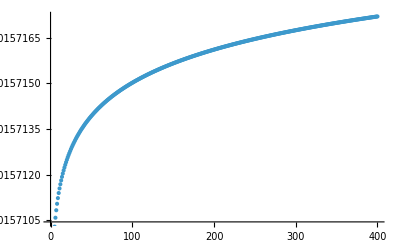

```mathematica
ListPlot[OmegaQuantization]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantization]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantization,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

1.600712206057902279706106821103293440192759656423292652421814867288806433108165989947250744936847×10^16-4.0753562946157059311132619089030218003456329960748423110365730557200116551902812363813094426080488×10^20 x+3.8908920103676156216243557179677172974715293551581042777633445879748951675490741463843659236816262×10^24 x^2-1.6510120840727997789116958387479307798217157497272271714487257586167568505547020738879130644793746×10^28 x^3+2.6271362274958897895453319209754186911017545970836408236436218574512338001124191344640245363553819×10^31 x^4

```mathematica
unfoldedE=spline[OmegaQuantization];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

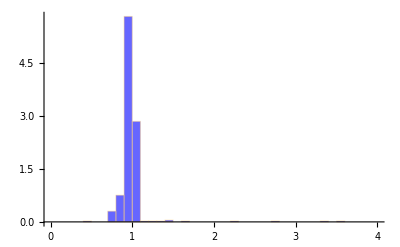

```mathematica
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantization]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

$Aborted

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-

Sigma=2

```mathematica
OmegaQuantizationtwo={};
For[i=1, i<=1000, i++,
Value=Values[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,2/Sqrt[i]],1] /.J->i,{ω,0.00015},WorkingPrecision->100]];
	OmegaQuantizationtwo=Append[OmegaQuantizationtwo,Value[[1]]]
]
```

FindRoot::precw: The precision of the argument function (-Sin[Arg[-1/(Gamma[«1»] Gamma[«1»] Gamma[«1»])]-Arg[Power[«2»] Power[«2»] Power[«2»]]]=={-Sin[19997.9 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (-Sin[Arg[-1/(Gamma[«1»] Gamma[«1»] Gamma[«1»])]-Arg[Power[«2»] Power[«2»] Power[«2»]]]=={-Sin[19998.4 ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (-Sin[Arg[-1/(Gamma[«1»] Gamma[«1»] Gamma[«1»])]-Arg[Power[«2»] Power[«2»] Power[«2»]]]=={-Sin[20002.5 ω]}) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::munfl: (-1.03958×10^-152-3.57084×10^-156 ⅈ) (1.0608×10^-154+4.5703×10^-158 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.03958×10^-152-4.47094×10^-156 ⅈ) (1.0608×10^-154-3.65184×10^-158 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.05147×10^-153-3.61573×10^-157 ⅈ) (1.06749×10^-155+4.60318×10^-159 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

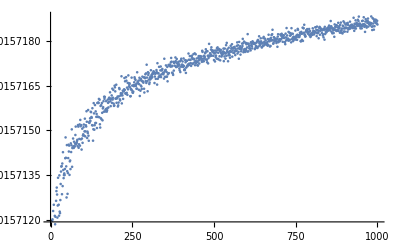

```mathematica
ListPlot[OmegaQuantizationtwo]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationtwo]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationtwo,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationtwo];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

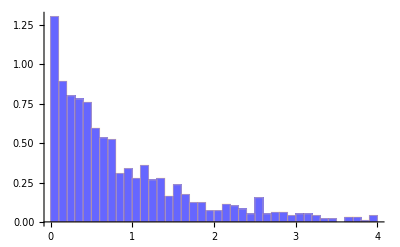

```mathematica
Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationtwo]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-

Sigma=0.025

```mathematica
OmegaQuantizationthree = {};
For[i=1, i<=1000, i++,
	Value=Values[FindRoot[Sin[alpha-beta]==Sin[2λ ω] /.λ->RandomVariate[NormalDistribution[-10^4,0.025/Sqrt[i]],1] /.J->i,{ω,0.00015},WorkingPrecision->100]];
	OmegaQuantizationthree=Append[OmegaQuantizationthree,Value[[1]]]
]
```

FindRoot::precw: The precision of the argument function (-Sin[Arg[-1/(Gamma[«1»] Gamma[«1»] Gamma[«1»])]-Arg[Power[«2»] Power[«2»] Power[«2»]]]=={-Sin[20000. ω]}) is less than WorkingPrecision (100.).

FindRoot::precw: The precision of the argument function (-Sin[Arg[-1/(Gamma[«1»] Gamma[«1»] Gamma[«1»])]-Arg[Power[«2»] Power[«2»] Power[«2»]]]=={-Sin[19999.9 ω]}) is less than WorkingPrecision (100.).

General::stop: Further output of FindRoot::precw will be suppressed during this calculation.

General::munfl: (-1.03958×10^-152-3.57084×10^-156 ⅈ) (1.0608×10^-154+4.5703×10^-158 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (1.03958×10^-152-4.47094×10^-156 ⅈ) (1.0608×10^-154-3.65184×10^-158 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (-1.05147×10^-153-3.61573×10^-157 ⅈ) (1.06749×10^-155+4.60318×10^-159 ⅈ) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

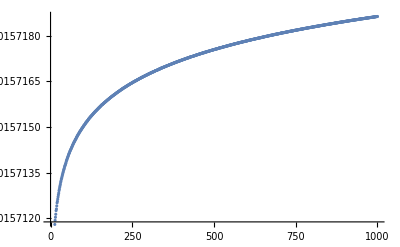

```mathematica
ListPlot[OmegaQuantizationthree]
```

```mathematica
cumulativeDOS=Range[Length[OmegaQuantizationthree]];
spline[x_]=Function[x,Fit[Transpose[{OmegaQuantizationthree,cumulativeDOS}], Table[x^n,{n,0,4}],x]][x];
```

```mathematica
unfoldedE=spline[OmegaQuantizationthree];

spacings=Differences[Sort[unfoldedE]];
```

```mathematica
meanSpacing=Mean[spacings];
normalizedSpacings=spacings/meanSpacing;
```

```mathematica
histogram=Histogram[normalizedSpacings,{0,4,.1},"PDF",ChartStyle->{Opacity[0.6,Blue]}];
```

```mathematica
wignerDyson[x_]:=(32/Pi^2) x^2 Exp[-(4/Pi) x^2];
wdPlot=Plot[wignerDyson[x],{x,0,3},PlotStyle->{Blue,Thick}];
```

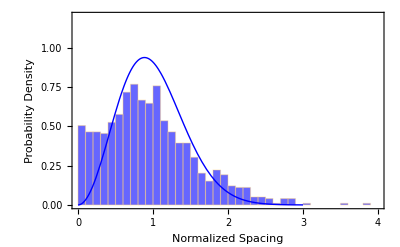

```mathematica
Show[histogram,wdPlot,PlotRange->{{0,4},{0,1.2}},AxesOrigin->{0,0},Frame->True,FrameLabel->{"Normalized Spacing","Probability Density"},PlotLegends->{"Data","Wigner-Dyson"}]
```

```mathematica
SFF[t_]=Abs[Total[Exp[ⅈ*t*OmegaQuantizationthree]]/400]^2;
plot=Array[SFF[#]&,1000000,{10^7,10^13}];
time=Array[#&,1000000,{10^7,10^13}];
```

$Aborted

```mathematica
ListPlot[Transpose[{time,plot}],PlotStyle->{Blue,Thick},ScalingFunctions->{"Log","Log"},PlotRange->{10^(-7),1}]
```

-Graphics-